# Domínio Harmônico Multifásico do GCSC

```mathematica
Clear["Global`*"]
```

Neste nb foi tratado somente o GCSC, observando a dualidade com o RCT. Ok.

## 1. Introdução

Referência Bibliográfica:
Tensorial Analysis of GCSC in a Very Long 750 kV Transmission Line
F.D.Jesus,R.F.S.Dias,M.Aredes,Member and E.H.Watanabe,Senior Member,IEEE

## 2. Dados do Sistema

### GCSC

```mathematica
cap=45.*10^-6;
ycap[ω1_]:=I*ω1*cap;
zcap[ω1_]:=1/(ycap[ω1]);
```

## 3. Número de Harmônicas, Número de Fases, Número de Barras e Frequência Base

```mathematica
nharm=50;
nfase=3;
nbarra=1;
ω=2*Pi*60;
ω1=ω;
s1=ⅉ k1 ω1;
α=2 π/3;
```

## 4. Função de Chaveamento

A  função de chaveamento foi desenvolvida para o chaveamento da corrente para o capacitor.

```mathematica
Sn[n_,γ_,ϕ_]:=If[n>0,-(2(1+(-1)^n)*Sin[n γ]*(Cos[n*ϕ]-ⅉ Sin[n*ϕ])/(n*Pi)),If[n==0,2-2 γ/Pi,0]];
DγSn[n_,γ_,ϕ_]:=If[n>0,-(2(1+(-1)^n)*Cos[n γ]*(Cos[n*ϕ]-ⅉ Sin[n*ϕ])/Pi),If[n==0,-2/Pi,0]];
(*DϕSn[n_,γ_,ϕ_]:=If[n>0,2(1+(-1)^n)*Sin[n γ]*(Sin[n*ϕ]+ⅉ Cos[n*ϕ])/Pi,0];*)
```

### Valores Iniciais

```mathematica
modi1=Sqrt[2./3]*50.;

ϕsin=-Pi/2.;         (*=== Senóide ===*)


α120=2*Pi/3.;            (*Defasagem entre fases *)
b=ConstantArray[0,{2 (nbarra+1) nfase nharm+1,1}];
b⟦nharm,1⟧=0.5 (modi1 Cos[ϕsin]-ⅈ modi1 Sin[ϕsin]);
b⟦nharm+1,1⟧=Conjugate[b⟦nharm,1⟧];
b⟦3 nharm,1⟧=0.5 (modi1 Cos[ϕsin-α120]-ⅈ modi1 Sin[ϕsin-α120]);
b⟦3 nharm+1,1⟧=Conjugate[b⟦3 nharm,1⟧];
b⟦5 nharm,1⟧=0.5 (modi1 Cos[α120+ϕsin]-ⅈ modi1 Sin[α120+ϕsin]);
b⟦5 nharm+1,1⟧=Conjugate[b⟦5 nharm,1⟧];

b⟦(2*nharm*nfase*(nbarra+1))+1,1⟧=γesp;
(*b⟦(2*nharm*nfase*(nbarra+1))+2,1⟧=ϕesp;

ϕesp=-π/2.;*)
γesp=(2 π)/3.;
auxΔi=ConstantArray[0,{2 nbarra nfase nharm,1}];
Underscript[Δiter, 1]:=auxΔi;
Underscript[viter, 1,1]:=Table[If[i==nharm,{-0.005+ⅈ 0.005},If[i==nharm+1,{-0.005-ⅈ 0.005},{0}]],{i,1,2 nharm}];
Underscript[viter, 1,2]:=Table[If[i==nharm,{-0.005+ⅈ 0.005},If[i==nharm+1,{-0.005-ⅈ 0.005},{0}]],{i,1,2 nharm}];
Underscript[viter, 1,3]:=Table[If[i==nharm,{-0.005+ⅈ 0.005},If[i==nharm+1,{-0.005-ⅈ 0.005},{0}]],{i,1,2 nharm}];
Underscript[γiter, 1]=Underscript[γiter, it]/.it->1;

Underscript[γiter, 1]=π/2.;
ϕitt=0;
Subscript[ϕvitt, 1][it_]:=Arg[Underscript[viter, it,1]⟦nharm+1,1⟧];
Subscript[ϕvitt, 2][it_]:=Arg[Underscript[viter, it,2]⟦nharm+1,1⟧];
Subscript[ϕvitt, 3][it_]:=Arg[Underscript[viter, it,3]⟦nharm+1,1⟧];
batual=ConstantArray[0,{2 (nbarra+1) nfase nharm+1,1}];

Do[batual⟦i,1⟧=If[i≤2 nbarra nfase nharm,Underscript[Δiter, it]⟦i,1⟧,If[i≤2 nharm (nbarra nfase+1),Underscript[viter, it,1]⟦i-2 nbarra nfase nharm,1⟧,If[i≤2 nharm (nbarra nfase+2),Underscript[viter, it,2]⟦i-2 nharm (nbarra nfase+1),1⟧,If[i≤2 (nbarra+1) nfase nharm,Underscript[viter, it,3]⟦i-2 nharm (nbarra nfase+2),1⟧,
Underscript[γiter, it]]]]],{i,1,2*nharm*nfase*(nbarra+1)+1}];
```

Part::partd: Part specification Δiter it ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification Δiter it ⟦ 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

Part::partw: Part 3 of Δiter it does not exist.

Part::partw: Part 4 of Δiter it does not exist.

Part::partw: Part 5 of Δiter it does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

## 6. Construção da Zbarra para o Sistema

```mathematica
Subscript[znodal, 1,1]=IdentityMatrix[2*nharm*nfase];
```

### Zbarra Estendida

i_C(t)=C (ⅆ v_C(t))/ⅆt
Com o chaveamento da corrente por uma função P, vem:
i_C(t)=p(t) i(t)⟹i_C=P i;
v_C(t)=1/C∫ i_C(t)ⅆt  ⟶ v_C(t)=1/C∫P. i(t)ⅆt ⟶ v_C=P 1/C 1/s P. i  ⟶ v_C=P 1/sC P. i  (I)

Lembrando que a integral  Snoda =diag{ⅉ k1ω}, onde k1=±k;
Z_sw=P.invS.1/CP

```mathematica
cc=ConstantArray[0,{1,2 nharm-1}];
Do[kk1=i;
cc[[1,i]]=If[i≤(nharm-1),0.5 Sn[2 kk1,Underscript[γiter, it],ϕit],0];Clear[kk1,i],
{i,1,2 nharm-1}];
cc1=Join[{{Sn[0,Underscript[γiter, it],ϕit]}},cc,2];
cc2[ϕit_]=cc1[[1,Range[2 nharm]]];

rr=ConstantArray[0,{1,2 nharm}];
Do[kk1=i;
rr[[1,i]]=If[i≤(nharm-1),Conjugate[0.5  Sn[2 kk1,Underscript[γiter, it],ϕit]],0];Clear[kk1,i],
{i,1,2 nharm-1}];
rr1=Join[{{Sn[0,Underscript[γiter, it],ϕit]}},rr,2];
rr2[ϕit_]=rr1[[1,Range[2 nharm]]];

P1=ToeplitzMatrix[cc2[ϕitt],rr2[ϕitt]];
P2=ToeplitzMatrix[cc2[ϕitt+α120],rr2[ϕitt+α120]];
P3=ToeplitzMatrix[cc2[ϕitt-α120],rr2[ϕitt-α120]];


Do[k1=If[i≤2nharm,2*(i-nharm)-1,0];Subscript[invS, i,j]=If[i==j,zcap[k1*ω1],0];Clear[k1],{i,1,2*nharm},{j,1,2*nharm}];

invS=ArrayFlatten[Table[Subscript[invS, i,j],{i,1,2*nharm},{j,1,2*nharm}]];

Subscript[P, 1]=P1.invS.P1;

Subscript[P, 2]=P2.invS.P2;

Subscript[P, 3]=P3.invS.P3;


znodal21=ConstantArray[0,{nfase,nfase}];

ky=If[p≤nfase,nfase,0];

Do[ky=If[i≤nfase,i,0];znodal21[[i,j]]=If[i==j,Subscript[P, i],ConstantArray[0,{2*nharm,2*nharm}]];Clear[ky],{i,1,nfase},{j,1,nfase}]


Subscript[znodal, 2,1]=ArrayFlatten[znodal21];


Subscript[znodal, 1,2]=ConstantArray[0,{2*nharm*nfase,2*nharm*nfase}];
Subscript[znodal, 2,2]=Subscript[znodal, 1,1];

zbarramod=ArrayFlatten[Table[Subscript[znodal, i,j],{i,1,nbarra+1},{j,1,nbarra+1}]];
```

(«1»)

(«1»)

(«1»)

«1 more identical outputs»

-Graphics-

## 7. Solução Iterativa

```mathematica
matΔγ1=ConstantArray[0,{(2*nharm*nfase*(nbarra+1)),1}];

matΔγ11=ConstantArray[0,{(2*nharm*nfase*(nbarra+1)),1}];

(*matΔϕ11=ConstantArray[0,{(2*nharm*nfase*(nbarra+1)),1}];*)

kini=0;
Do[iz=Quotient[kini,2*nharm]+1;kini=i-2*nfase*nharm*nbarra;
kk=If[kini≤2*nharm,(2*(kini-nharm)-1),If[kini≤4*nharm,(2*(kini-3 nharm)-1),If[kini≤6*nharm,(2*(kini-5 nharm)-1),0]]];
matΔγ1[[i,1]]=If[iz==1,DγSn[ kk,Underscript[γiter, it],ϕitt],If[iz==2,DγSn[ kk,Underscript[γiter, it],ϕitt-α120],If[iz==3,DγSn[ kk,Underscript[γiter, it],ϕitt+α120],0]]];Clear[iz,kk],
{i,2*nfase*nharm*nbarra+1,2*nfase*nharm*(nbarra+1)}];


matΔγ2={Table[If[i==(2*nharm*nfase*(nbarra+1))+1,1,0],{i,1,(2*nharm*nfase*(nbarra+1))+1}]};

(*matΔϕ1=ConstantArray[0,{(2*nharm*nfase*(nbarra+1)),1}];


kini=0;
Do[iz=Quotient[kini,2*nharm]+1;kini=i-2*nfase*nharm*nbarra;
kk=If[kini≤2*nharm,(2*(kini-nharm)-1),If[kini≤4*nharm,(2*(kini-3 nharm)-1),If[kini≤6*nharm,(2*(kini-5 nharm)-1),0]]];ϕvit=Subscript[ϕvitt, iz][it];
matΔϕ1[[i,1]]=If[iz==1,DϕSn[ kk,γiter_it,ϕit_it],If[iz==2,DϕSn[ kk,γiter_it,ϕit_it-α120],If[iz==3,DϕSn[ kk,γiter_it,ϕit_it+α120],0]]];Clear[iz,kk,ϕvit],{i,2*nfase*nharm*nbarra+1,2*nfase*nharm*(nbarra+1)}];
matΔϕ2={Table[If[i==(2*nharm*nfase*(nbarra+1)+2),1,0],{i,1,(2*nharm*nfase*(nbarra+1))+2}]};*)

matΔγ3:=Join[zbarramod,matΔγ1,2];(*AppendRows:Aumenta o número de colunas*)
zbarramod1:=Join[matΔγ3,matΔγ2];

matΔγ4:=Join[zbarramod,matΔγ11,2];
zbarramod2:=Join[matΔγ4,matΔγ2];

MatrixPlot[zbarramod1/.it->1, ColorFunction->"Monochrome"]
MatrixPlot[zbarramod1/.it->1, ColorFunction->"Monochrome", Mesh->True]
MatrixPlot[zbarramod2/.it->1, ColorFunction->"Monochrome"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
mismatch=1;
For[it=1,Max[Abs[mismatch]]>10^-9∧it≤50,it++,

mismatch=b-zbarramod2.batual;
vetor=LinearSolve[zbarramod1,mismatch];

Underscript[Δiter, it+1]=Underscript[Δiter, it]+vetor[[Range[1,2*nharm*nfase*nbarra]]];
Underscript[viter, it+1,1]=Underscript[viter, it,1]+vetor[[Range[2*nharm*nfase*nbarra+1,2*nharm*(nfase*nbarra+1)]]];
Underscript[viter, it+1,2]=Underscript[viter, it,2]+vetor[[Range[2*nharm*(nfase*nbarra+1)+1,2*nharm*(nfase*nbarra+2)]]];
Underscript[viter, it+1,3]=Underscript[viter, it,3]+vetor[[Range[2*nharm*(nfase*nbarra+2)+1,2*nharm*nfase*(nbarra+1)]]];
Underscript[γiter, it+1]=Underscript[γiter, it]+vetor[[2*nharm*nfase*(nbarra+1)+1,1]]];
```

```mathematica
Max[Abs[mismatch]]
Underscript[γiter, it] 180./π
Subscript[ϕvitt, 1][it] 180./π
Subscript[ϕvitt, 2][it] 180./π
Subscript[ϕvitt, 3][it] 180./π
it
```

7.20403×10^-13

120.+0. ⅈ

3.50835×10^-15

-120.

120.

4

## 8. Análise Gráfica

```mathematica
posicao1=1;
Do[Subscript[vca, i]=Underscript[viter, it,1][[posicao1,1]];posicao1++,{i,-(2*nharm-1),2*nharm,2}];
vca=Sum[Re[Subscript[vca, i]]*Cos[i*ω*t]-Im[Subscript[vca, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];

posicao2=1;
Do[Subscript[vcb, i]=Underscript[viter, it,2][[posicao2,1]];posicao2++,{i,-(2*nharm-1),2*nharm,2}];
vcb=Sum[Re[Subscript[vcb, i]]*Cos[i*ω*t]-Im[Subscript[vcb, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];

posicao3=1;
Do[Subscript[vcc, i]=Underscript[viter, it,3][[posicao3,1]];posicao3++,{i,-(2*nharm-1),2*nharm,2}];
vcc=Sum[Re[Subscript[vcc, i]]*Cos[i*ω*t]-Im[Subscript[vcc, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];
```

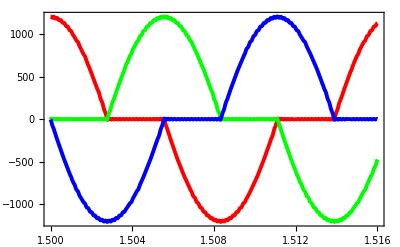

```mathematica
Plot[{vca,vcb,vcc},{t,1.5,1.516},Frame->True,PlotStyle->{{RGBColor[1,0,0],Thickness[0.007]},{RGBColor[0,1,0],Thickness[0.007]},{RGBColor[0,0,1],Thickness[0.007]}}]
```

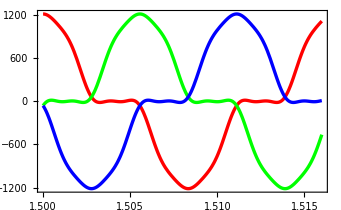
```mathematica
(* -Graphics-  Resposta Análise Tensorial*)
```

```mathematica
posicao=1;
(*If[posicao≤2*nharm*nfase*nbarra,*)
Do[Subscript[i, barra,fase,i]=Underscript[Δiter, it][[posicao,1]];posicao++,{barra,1,nbarra},{fase,1,nfase},{i,-(2*nharm-1),2*nharm,2}];

ia=Sum[Re[Subscript[i, 1,1,i]]*Cos[i*ω*t]-Im[Subscript[i, 1,1,i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];
ib=Sum[Re[Subscript[i, 1,2,i]]*Cos[i*ω*t]-Im[Subscript[i, 1,2,i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];
ic=Sum[Re[Subscript[i, 1,3,i]]*Cos[i*ω*t]-Im[Subscript[i, 1,3,i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];

iam=Underscript[Δiter, it][[Range[1,2*nharm]]];
ibm=Underscript[Δiter, it][[Range[1+2*nharm,4*nharm]]];
icm=Underscript[Δiter, it][[Range[1+4*nharm,6 nharm]]];
```

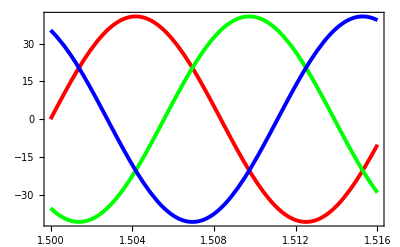

```mathematica
Plot[{ia, ib,ic},{t,1.5,1.516},PlotPoints->50,Frame->True,PlotStyle->{{RGBColor[1,0,0],Thickness[0.007]},{RGBColor[0,1,0],Thickness[0.007]},{RGBColor[0,0,1],Thickness[0.007]}}]
```

```mathematica
igcsca=(IdentityMatrix[2 nharm]-P1).iam;
igcscb=(IdentityMatrix[2 nharm]-P2).ibm;
igcscc=(IdentityMatrix[2 nharm]-P3).icm;
posicao11=1;
Do[Subscript[igcsca, i]=igcsca[[posicao11,1]];posicao11++,{i,-(2*nharm-1),2*nharm,2}];
igcscat=Sum[Re[Subscript[igcsca, i]]*Cos[i*ω*t]-Im[Subscript[igcsca, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];

posicao12=1;
Do[Subscript[igcscb, i]=igcscb[[posicao12,1]];posicao12++,{i,-(2*nharm-1),2*nharm,2}];
igcscbt=Sum[Re[Subscript[igcscb, i]]*Cos[i*ω*t]-Im[Subscript[igcscb, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];

posicao13=1;
Do[Subscript[igcscc, i]=igcscc[[posicao13,1]];posicao13++,{i,-(2*nharm-1),2*nharm,2}];
igcscct=Sum[Re[Subscript[igcscc, i]]*Cos[i*ω*t]-Im[Subscript[igcscc, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];
```

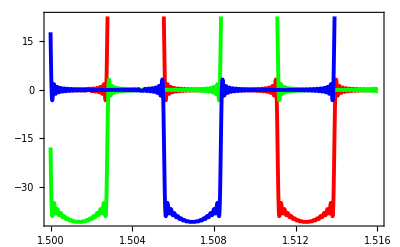

```mathematica
Plot[{igcscat,igcscbt,igcscct},{t,1.5,1.516},Frame->True,PlotStyle->{{RGBColor[1,0,0],Thickness[0.007]},{RGBColor[0,1,0],Thickness[0.007]},{RGBColor[0,0,1],Thickness[0.007]}}]
```

```mathematica
vca1=Subscript[P, 1].iam;
vcb1=Subscript[P, 2].ibm;
vcc1=Subscript[P, 3].icm;
posicao14=1;
Do[Subscript[vca, i]=vca1[[posicao14,1]];posicao14++,{i,-(2*nharm-1),2*nharm,2}];
vcat=Sum[Re[Subscript[vca, i]]*Cos[i*ω*t]-Im[Subscript[vca, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];

posicao15=1;
Do[Subscript[vcb, i]=vcb1[[posicao15,1]];posicao15++,{i,-(2*nharm-1),2*nharm,2}];
vcbt=Sum[Re[Subscript[vcb, i]]*Cos[i*ω*t]-Im[Subscript[vcb, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];

posicao16=1;
Do[Subscript[vcc, i]=vcc1[[posicao16,1]];posicao16++,{i,-(2*nharm-1),2*nharm,2}];
vcct=Sum[Re[Subscript[vcc, i]]*Cos[i*ω*t]-Im[Subscript[vcc, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];
```

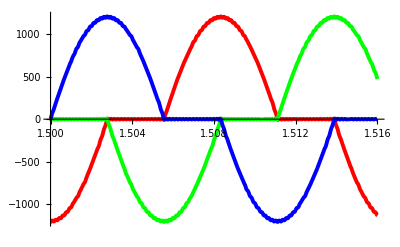

```mathematica
Plot[{vcat,vcbt,vcct},{t,1.5,1.516},PlotStyle->{{RGBColor[1,0,0],Thickness[0.007]},{RGBColor[0,1,0],Thickness[0.007]},{RGBColor[0,0,1],Thickness[0.007]}}]
```

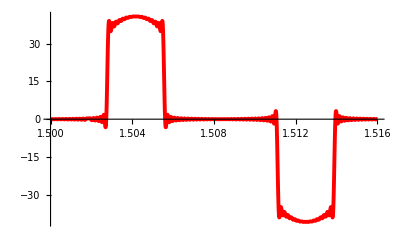

```mathematica
Plot[{igcscat},{t,1.5,1.516},PlotStyle->{{RGBColor[1,0,0],Thickness[0.007]},{RGBColor[0,1,0],Thickness[0.007]},{RGBColor[0,0,1],Thickness[0.007]}}]
```

```mathematica
igtoa=P1.iam;
igtob=P2.ibm;
igtoc=P3.icm;
posicao17=1;
Do[Subscript[igtoa, i]=igtoa[[posicao17,1]];posicao17++,{i,-(2*nharm-1),2*nharm,2}];
igtoat=Sum[Re[Subscript[igtoa, i]]*Cos[i*ω*t]-Im[Subscript[igtoa, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];

posicao18=1;
Do[Subscript[igtob, i]=igtob[[posicao18,1]];posicao18++,{i,-(2*nharm-1),2*nharm,2}];
igtobt=Sum[Re[Subscript[igtob, i]]*Cos[i*ω*t]-Im[Subscript[igtob, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];

posicao19=1;
Do[Subscript[igtoc, i]=igtoc[[posicao19,1]];posicao19++,{i,-(2*nharm-1),2*nharm,2}];
igtoct=Sum[Re[Subscript[igtoc, i]]*Cos[i*ω*t]-Im[Subscript[igtoc, i]]*Sin[i*ω*t],{i,-(2*nharm-1),2*nharm,2}];
```

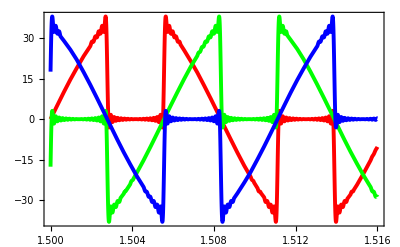

```mathematica
Plot[{igtoat,igtobt,igtoct},{t,1.5,1.516},Frame->True,PlotStyle->{{RGBColor[1,0,0],Thickness[0.007]},{RGBColor[0,1,0],Thickness[0.007]},{RGBColor[0,0,1],Thickness[0.007]}}]
```

```mathematica
Plot[{igcscat+igtoat, igcscbt+igtobt,igcscct+igtoct},{t,1.5,1.516}, Frame->True, PlotStyle->{{RGBColor[1,0,0],Thickness[0.007]},{RGBColor[0,1,0],Thickness[0.007]},{RGBColor[0,0,1],Thickness[0.007]}}]
```

-Graphics-

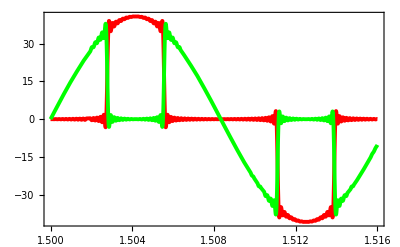

```mathematica
Plot[{igcscat,igtoat},{t,1.5,1.516},Frame->True,PlotStyle->{{RGBColor[1,0,0],Thickness[0.007]},{RGBColor[0,1,0],Thickness[0.007]},{RGBColor[0,0,1],Thickness[0.007]}}]
```

```mathematica
Date[]
```

{2010,8,7,14,24,41.616294}